```mathematica
(*считываем битовый сигнал, переводим в аналог*)
t = 3.75;
discretSignal = ReadList["C:\\Users\\22153\\Documents\\leti\\foit\\IDZ4\\signal\\signaldigit18.txt", {Number, Number, Number, Number, Number, Number, Number, Number}];
analogSignal =Table[FromDigits[discretSignal[[i]], 2], {i, 1, Length@discretSignal}]
dt = t/ Length@discretSignal;
ListPlay[analogSignal, SampleRate->44100]
```

-Graphics-

-----------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
(*строю график сигнала*)
ForPlot=Table[{(i-1)*dt, analogSignal[[i]]},{i,1, Length@discretSignal}];
ListPlot[ForPlot, Filling->Axis,PlotRange->Full]
```

-Graphics-

-----------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
(*нахожу спектр*)
Fsig=Fourier[analogSignal];
outN=Length@Fsig;
df=1/t;

FourAbs=Table[{2π df (i-1), Abs@Fsig[[i]]},{i,2,outN}];

ListPlot[FourAbs, Filling->Axis,PlotRange->Full]
```

-Graphics-

-----------------------------------------------------------------------------------------------------------------------------------------------------

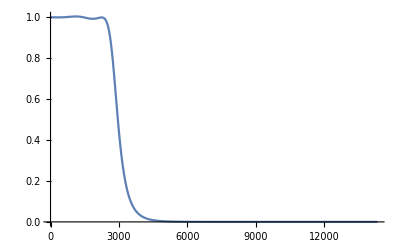

```mathematica
(*пытаюсь сделать фильтр Батерворта*)
coef = 2.25;
R1 =50;
C1 = 0.0000059*coef;
C2 = 0.0000054*coef;
C3 = 0.0000041*coef;
C4 = 0.0000024*coef;
C5 = 497.9 * 10^-9*coef;
L1 = 0.0124*coef;
L2 = 0.0144*coef;
L3 = 0.012*coef;
L4 = 0.0083*coef;
L5 = 0.0037*coef;

Zpar5[w_] = 1/(I w C5+1/R1);
Zpar4[w_] = 1/(I w C4+1/(I w L5 + Zpar5[w]));
Zpar3[w_] = 1/(I w C3+1/(I w L4 + Zpar4[w]));
Zpar2[w_] = 1/(I w C2+1/(I w L3 + Zpar3[w]));
Zpar[w_] = 1/(I w C1+1/(I w L2 + Zpar2[w])); (*общий*)
I1[w_] = Uin/(I w L1 + Zpar[w]);

Upar[w_] = I1[w]*Zpar[w];
I2[w_] = Upar[w]/(I w L2 + Zpar2[w]);

Upar2[w_] = I2[w] * Zpar2[w];
I3[w_] = Upar2[w]/(I w L3+ Zpar3[w]);

Upar3[w_] = I3[w] * Zpar3[w];
I4[w_] = Upar3[w]/(I w L4+ Zpar4[w]);

Upar4[w_] = I4[w] * Zpar4[w];
I5[w_] = Upar4[w]/(I w L5+ Zpar5[w]);

Upar5[w_] = I5[w] * Zpar5[w];
Uout[w_] = Upar5[w];

H[w_]= Uout[w]/Uin;

Hlist=Table[Abs@H[i],{i,1,outN}];
Fnew = Fsig*Hlist;

Plot[Abs@H[w],{w, 1, outN/10}, PlotRange->Full]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
(*смотрю преобразованный спектр*)
FnewTable=Table[{2π df (i-1), Abs@Fnew[[i]]},{i,2,outN}];

ListPlot[FnewTable, Filling->Axis,PlotRange->Full]
```

-Graphics-

-----------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
(*получаю обратно сигнал*)
ChangedSignal=InverseFourier[Fnew];

FilteredSignal=Table[{( i-1)*dt,Re@ChangedSignal[[i]]},{i,1,Length@discretSignal}];

ListPlot[FilteredSignal,Filling->Axis,PlotRange->Full]
```

-Graphics-

-----------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
(*воспроизвожу*)
ListPlay[Re@ChangedSignal, SampleRate->44100]
```

-Graphics-